# Sequence and series of numbers

## Sequence

```mathematica
a[n_]:=1/n^2
```

```mathematica
(*1/n^2, 1/2^n, (-1)^(n+1)/n*)
```

```mathematica
nb:=5
```

```mathematica
list:=Table[{n,a[n]},{n,1,nb}]
```

```mathematica
TableForm[list,TableHeadings->{None,{"n","a[n]"}}]
```

n | a[n]
1 | 1
2 | 1/4
3 | 1/9
4 | 1/16
5 | 1/25

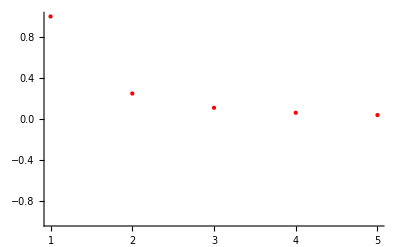

```mathematica
ListPlot[Table[{n,a[n]},{n,1,nb}],PlotStyle->Directive[PointSize[Large],Red],PlotRange->{-1,1}]
```

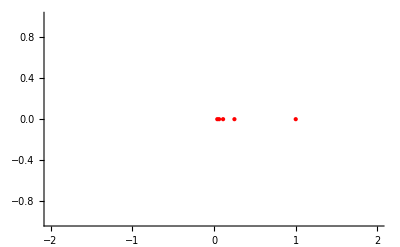

```mathematica
ListPlot[Table[{a[n],0},{n,1,nb}],PlotStyle->Directive[PointSize[Large],Red],PlotRange->{{-2,2},{-1,1}}]
```

## Series

```mathematica
series:=Table[{k,∑_(n=1)^k a[n]},{k,1,nb}]
```

```mathematica
TableForm[series,TableHeadings->{None,{"k","∑_(n = 1)^k a[n]"}}]
```

k | ∑_(n = 1)^k a[n]
1 | 1
2 | 5/4
3 | 49/36
4 | 205/144
5 | 5269/3600

```mathematica
SumConvergence[a[n],n]
```

True

```mathematica
∫_1^∞ a[n]ⅆn
```

1

```mathematica
∑_(n=1)^∞ a[n]
```

π^2/6

```mathematica
plot1:=ListPlot[series,PlotStyle->Directive[PointSize[Large],Red]]

plot2:=Plot[Sum[a[n],{n,1,∞}],{x,0,nb}]
```

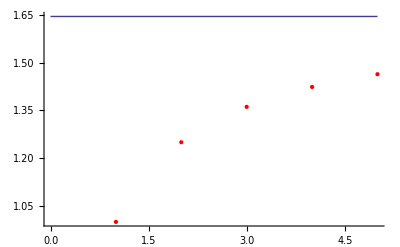

```mathematica
Show[plot1,plot2]
```